```mathematica
Remove["Global`*"];
```

```mathematica
data=Import["C:\\Users\\Jim\\Documents\\Ma191b\\spinglassmodel\\SG2LTHEdata.txt","Table"];
```

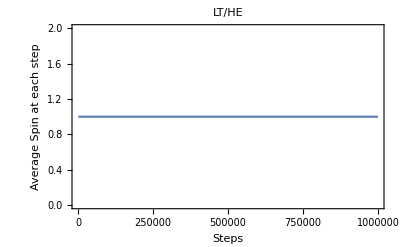

```mathematica
justdata=data[[2;;-1,1;;2]];ListLinePlot[justdata,PlotLabel->"LT/HE", Frame->True,
FrameLabel->{"Steps","Average Spin at each step"}]
```

```mathematica
data2=Transpose[data];
justdata2=data2[[1;;-1,2;;-1]];justjustdata2=Drop[justdata2,{2}];justjustjustdata2=Transpose[justjustdata2];ListLinePlot[justjustjustdata2,PlotLabel->"LT/HE", Frame->True,
FrameLabel->{"Steps","Average Spin at each step"}]
```

-Graphics-